# Lecture 10 - Electric Potential

### A Puzzle...

#### The Slab

At the end of last class, we considered the electric field from a slab (and infinite sheet with thickness d) that has uniform charge density ρ. Suppose we know that the electric field has magnitude E_1 a distance x_1 from the middle of the slab. What is the magnitude of the electric field E_2 at a distance x_2?

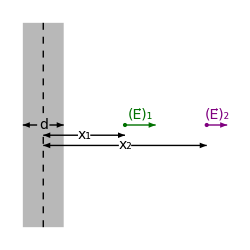

```mathematica
s=0.3;
centerPlot@Graphics[{{GrayLevel[0.72],Rectangle[{0,-5},{2,5}]},Arrowheads[0.03],Text[font["d",Italic],{1,0}],Text[font["x_1"],{3,-0.5}],Text[font["x_2"],{5,-1}],{Darker@Darker@Green,Point[{5,0}],Arrow[{{5,0},{6.5,0}}],Text[font@"(E⃗)_1",{5.75,0.5}]},{Purple,Point[{9,0}],Arrow[{{9,0},{10,0}}],Text[font@"(E⃗)_2",{9.5,0.5}]},Arrow[{{{1-s,0},{0,0}},{{1+s,0},{2,0}}}],Arrow[{{{3-s,-0.5},{1,-0.5}},{{3+s,-0.5},{5,-0.5}}}],Arrow[{{{5-s,-1},{1,-1}},{{5+s,-1},{9,-1}}}],Dashed,Line[{{{1,-5},{1,-0.5}},{{1,5},{1,0.5}}}]},ImageSize->250]
```

Solution
Recall from last time that one way to think about the slab is as a composition of many thin sheets glued together. Since a thin sheet has an electric field σ/ϵ_0 pointing outwards away from it, and this electric field does not depend on distance, then gluing a bunch of these thin sheets together to make the full slab implies that E_1=E_2.

Note that inside the slab (when x_1<d/2), the electric field will no longer be constant, since the electric field contribution from the thin sheets to the left of x_1 will be partially canceled by the electric field from the thin sheets to the right of x_1. Indeed, at the center we know that E=0 by symmetry, and furthermore that the electric field at a distance x_1 must have the same magnitude (and opposite direction) of the electric field at -x_1. □

### Theory

#### An Analogy with Gravity

Before discussing the electric potential, let’s quickly recap some facts about the gravitational potential U=m g z near Earth. More specifically, the gravitational potential U

Is a scalar, representing the work done to move a mass m from ground level to a height z. This quantity is path independent - all that matters are the initial and final heights of the mass

The gravitational force F⃗=m g (-ẑ)=-(∂U)/(∂x)x̂-(∂U)/(∂y)ŷ-(∂U)/(∂z)ẑ=-OverVector[∇]U where OverVector[∇]=∂/(∂x)x̂+∂/(∂y)ŷ+∂/(∂z)ẑ is called the Del operator

We can invert the last statement and write the gravitational potential in terms of the line integral of the gravitational force U=-∫_P_1^P_2 F⃗·ⅆ s⃗

F⃗ points from regions of large U to small U (in the direction along which a mass released from rest will move)

Gravity far from Earth is given by F⃗=(G M m)/r^2 (-r̂) with potential U=-(G M m)/r. All of the above statements hold for this exact form of the gravitational force, and the 1/r^2 r̂ dependence in the force exactly mirrors the 1/r^2 r̂ dependence in Coulomb’s force, which tells us that the electric potential that we will define momentarily will also behave as 1/r

As with all energies, we can set the zero point of U to be anywhere we like. For gravity far from Earth, we typically choose the reference point U=0 at r=∞

#### Potential

All of the statements mentioned above hold for the case of electricity, once we replace the gravitational force with the electric field (F⃗→E⃗) and the gravitational potential with the electric potential (U→ϕ). In other words, we define the electric potential ϕ to be:

A scalar, representing the work per unit charge to move a point charge q from P_1 to P_2. The electric potential is path independent - all that matters are the initial and final points of the charge

The electric field and the electric potential can be written in terms of one another as

E⃗=-OverVector[∇]ϕ

ϕ=-∫_P_1^P_2 E⃗·ⅆ s⃗

E⃗ points from regions of large ϕ to small ϕ (in the direction along which a positive charge released from rest will move)

Drawing upon the analogy with the gravitational force far from Earth, the electric field and potential for point charges is given by

E⃗=∑_j (k q_j)/r_j^2(r̂)_j

ϕ=∑_j (k q_j)/r_j

As we have seen with the electric field, using the Principle of Superposition we can decompose a charge distribution into small chunks, each of which behaves like a point charge, leading to the following results for a charge distribution

E⃗=∫(k ⅆq)/r^2 r̂

ϕ=∫(k ⅆq)/r

As with all energies, we can set the zero point of ϕ to be anywhere we like. Unless a charge distribution goes out to ∞, it is usually convenient to see the zero potential out at infinity. However, when a charge distribution (like the infinite cylindrical shell) goes out to infinity, we will revert to the ϕ=-∫_P_1^P_2 E⃗·ⅆ s⃗ formulation of the electric potential which specifies the potential at a point P_2 relative to the potential at P_1

Visually, the fact that E⃗=-OverVector[∇]ϕ implies that the electric field points in the direction in which the potential decreases the fastest. Additionally, if we consider surfaces everywhere in space such that these surfaces are always tangent to the electric field lines at every point, then these surfaces will be equipotential, which means that the potential everywhere on the surface will be constant. The following diagram show the electric field lines and equipotential surfaces for a uniformly charged disk (shown from the side). To understand the full 3D picture, we would have to rotate this image about the y-axis.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

### Visualizing the Electric Potential

You may recall this Mathematica Manipulate from a few weeks ago. Let’s apply what we have learned and predict what the Electric Potential will look like for various setups.

```mathematica
arrowSize=5;
labels={"    Electric Field    ","     More +     ","     More -     ","Electric Potential","     Less +     ","     Less -     "};
{numPos,numNeg}={1,1};
centerPlot@Manipulate[
If[MemberQ[opts,labels[[2]]],numPos++;opts=DeleteCases[opts,labels[[2]]]];
If[MemberQ[opts,labels[[3]]],numNeg++;opts=DeleteCases[opts,labels[[3]]]];
If[MemberQ[opts2,labels[[5]]],numPos--;opts2=DeleteCases[opts2,labels[[5]]]];
If[MemberQ[opts2,labels[[6]]],numNeg--;opts2=DeleteCases[opts2,labels[[6]]]];
positive={p1,p3,p5,p7}[[;;numPos]];
negative={p2,p4,p6,p8}[[;;numNeg]];
arrow=Table[{GrayLevel[Clip[Norm[Total[({x,y}-#)/Norm[{x,y}-#]^3&/@positive]-Total[({x,y}-#)/Norm[{x,y}-#]^3&/@negative]]^(1/3),{0,0.004^(1/3)}]/0.004^(1/3)],Arrow[{{x,y}-0.6arrowSize(Normalize[Total[({x,y}-#)/Norm[{x,y}-#]^3&/@positive]-Total[({x,y}-#)/Norm[{x,y}-#]^3&/@negative]]),{x,y}+2.2arrowSize(Normalize[Total[({x,y}-#)/Norm[{x,y}-#]^3&/@positive]-Total[({x,y}-#)/Norm[{x,y}-#]^3&/@negative]])}]},{x,-90,90,22},{y,-90,90,22}];
arrowPoints=Flatten[Table[{x,y},{x,-90,90,22},{y,-90,90,22}],1];
Show[Graphics[{{Black,Rectangle[{-100,-100},{100,100}]}},PlotRange->100,ImageSize->{400,400}],If[MemberQ[opts2,labels[[4]]],ContourPlot[Total[1/Norm[{x,y}-#]&/@positive]-Total[1/Norm[{x,y}-#]&/@negative],{x,-100,100},{y,-100,100},Contours->20,ClippingStyle->Automatic,ColorFunction -> (Blend[{Darker@Blue,Black,Darker@Red},#]&),Frame->False,ImageSize->{400,400}],Sequence@@{}],If[MemberQ[opts,labels[[1]]],Graphics[{{Thickness[0.013],Arrowheads[{0.01,0.045}],arrow,{Black,PointSize[0.002],Point[arrowPoints]}}},PlotRange->100,ImageSize->{400,400}],Sequence@@{}],Graphics[{{Lighter@Red,PointSize[0.04],Point[#],White,Text[Style["+",20,Bold],#+{0.3,0.5}]}&/@positive,{Lighter@Blue,PointSize[0.04],Point[#],White,Text[Style["-",20,Bold],#+{0.3,0.5}]}&/@negative}]],
{{opts,{labels[[1]]},"     "},labels[[1;;3]],ControlType->TogglerBar,Appearance->"Row"},{{opts2,{labels[[4]]},"     "},labels[[4;;6]],ControlType->TogglerBar,Appearance->"Row"},
{{p1,{8.5,8.5}},Locator,Appearance->None},{{p2,-13{1,1}},Locator,Appearance->None},
{{p3,RandomReal[{-50,50},2]},Locator,Appearance->None},{{p4,RandomReal[{-50,50},2]},Locator,Appearance->None},
{{p5,RandomReal[{-50,50},2]},Locator,Appearance->None},{{p6,RandomReal[{-50,50},2]},Locator,Appearance->None},
{{p7,RandomReal[{-50,50},2]},Locator,Appearance->None},{{p8,RandomReal[{-50,50},2]},Locator,Appearance->None},Paneled->False]
```

Note that the electric field lines (i.e. the arrows) always point perpendicular to the electric field contours.

This is why it takes zero work to move a charge along one of these contours (i.e. equipotential lines)

### Problems

#### Potential from a Point Charge

Example
What is the potential at a distance R from a point charge q?

Solution
Assume that the point charge lies at the origin. The general formula

ϕ=∑_j (k q_j)/r_j

reduces to

ϕ=(k q)/R

If you wanted to be hard core and do the integral in Equation (TextNumbered) using the reference point P_1=∞, then consider bringing the charge radially inward from ∞. So we want to compute

ϕ=-∫_∞^r E⃗·ⅆ s⃗

With such integrals, it is easy to get extremely confused about the sign, so let’s reverse the integration bounds so that we obtain the much more intuitive path from r to ∞ (which flips the sign of the integral),

ϕ=∫_r^∞ E⃗·ⅆ s⃗

This integral is straightforward. Assume the charge q lies at the origin and integrate along the radial path s⃗=r r̂ where r∈[R,∞].

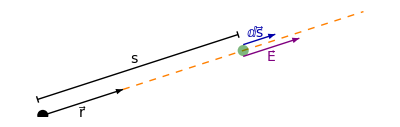

```mathematica
p={Cos[π/10],Sin[π/10]};pPerp=RotationMatrix[π/2].p;origin={0,0};
{a1,a2}={0.2,0.2};
centerPlot@Graphics[{Arrowheads[0.03],PointSize[0.02],Point[origin],Arrow[{origin,p}],{Dashed,Orange,Line[{p,4p}]},{Line[{{origin+a1 pPerp,2.5p+a1 pPerp},{(1+a2)a1 pPerp,(1-a2)a1 pPerp},{2.5p+(1+a2)a1 pPerp,2.5p+(1-a2)a1 pPerp}(*,{2.52p+(1+a2)a1 pPerp,2.52p+(1-a2)a1 pPerp}*)(*,{2.52p+a1 pPerp,2.7p+a1 pPerp}*)(*,{2.7p+(1+a2)a1 pPerp,2.7p+(1-a2)a1 pPerp}*)}]},{Darker@Darker@Green,Opacity[0.5],Point[2.5p]},Text[font["r⃗",14],p/2+{0,-0.12}],{Darker@Blue,Arrow[#+{0,0.07}&/@{2.5p,2.9p}],Text[font["ⅆs⃗",14],2.7p+{-0.05,0.15}]},{Purple,Arrow[#+{0,-0.07}&/@{2.5p,3.2p}],Text[font["E⃗",14],2.85p+{0.0,-0.18}]},Text[font["s",Italic,14],1.25p+a1 pPerp+{-0.05,0.1}]}]
```

Then E⃗=(k q)/r^2 r̂ and ⅆ s⃗=(ⅆr)r̂ so that

ϕ=∫_R^∞ (k q)/r^2 ⅆs=(k q)/R

If you want to integrate Equation (TextNumbered) directly, the key insight is that the integrand does not change: E⃗=(k q)/r^2 r̂ and ⅆ s⃗=ⅆr r̂. However, since we are now integrating from r∈[∞,R], ⅆr is now a negative quantity so that indeed ⅆ s⃗ points radially inwards as we expect. Thus we find

ϕ=-∫_∞^R (k q)/r^2 ⅆs=(k q)/R

in agreement with Equation (TextNumbered). □

#### Potential of a Spherical Shell

Example
A spherical shell has radius R and charge Q distributed uniformly across it. What is the potential a distance r from the center of the sphere:

Outside the sphere r>R?

Insider the sphere r<R?

Solution
Orient the center of the sphere at the origin. To best capitalize on the spherical symmetry, we will compute the potential at a point (0,0,z) on the z-axis. Because of the spherical symmetry, this must also be the potential at any point a distance r=z from the center of the sphere.

-Graphics-

Using the Law of Cosines, the distance from (0,0,z) to an infinitesimal patch on the sphere at the polar angle θ is (R^2+z^2-2R z Cos[θ])^(1/2). Using the uniform charge density σ=Q/(4π R^2), the potential at (0,0,z) is given by

V=∫_0^(2π) ∫_0^π (k (σ R^2 Sin[θ]ⅆθⅆϕ))/((R^2+z^2-2R z Cos[θ])^(1/2))
=2π k σ R^2∫_0^π (Sin[θ]ⅆθ)/((R^2+z^2-2R z Cos[θ])^(1/2))
=2π k σ R^2 {1/(R z)(R^2+z^2-2R z Cos[θ])^(1/2)}_(θ=0)^(θ=π)
=(2π k σ R)/z{(R^2+z^2+2R z)^(1/2)-(R^2+z^2-2R z)^(1/2)}
=(2π k σ R)/z{(R+z)-|R-z|}

Note that this integral must be evaluated separately for the cases z<R and z>R. In these two cases we find

V=Piecewise[{{4π k σ R, z<R}, {(4π k σ R^2)/z, z>R}}]

Using σ=Q/(4π R^2), we find

V=Piecewise[{{(k Q)/R, z<R}, {(k Q)/z, z>R}}]

Here are these two results confirmed by Mathematica,

```mathematica
Assuming[0<z<R,Integrate[(k R^2 Sin[θ]σ)/((R^2+z^2-2R z Cos[θ])^(1/2)),{θ,0,π},{ϕ,0,2π}]]/.σ->Q/(4π R^2)
Assuming[0<R<z,Integrate[(k R^2 Sin[θ]σ)/((R^2+z^2-2R z Cos[θ])^(1/2)),{θ,0,π},{ϕ,0,2π}]]/.σ->Q/(4π R^2)
```

(k Q)/R

(k Q)/z

Before analyzing these two remarkable results, let us first note that by the radial symmetry of this setup, we could just as well have oriented the z-axis to point in any direction, and hence these results apply to any point at a distance r from the center of the spherical shell,

V=Piecewise[{{(k Q)/R, r<R}, {(k Q)/r, r>R}}]

In hindsight, both of these results can quickly be found without writing down any integrals. First, the result (k Q)/r for r>R matches the potential from a point charge found in the example right above. This makes sense, since we have already seen by Gauss’s Law that the electric field outside of a spherical shell with charge Q distributed uniformly across it is identical to the electric field of a point charge Q at the center of the spherical shell. So if the electric field is the same everywhere outside the spherical shell, then the potential ϕ=-∫_∞^P E⃗·ⅆ s⃗ must also be the same for every point P outside the shell. So you can instantly recall that the potential outside a spherical shell will be (k Q)/r.

Next, recalling that the electric field inside a spherical shell is zero (if you don’t remember this, it is simple to verify using Gauss’s Law), then since the potential satisfies E⃗=-OverVector[∇]ϕ the potential must be constant everywhere inside the sphere. Furthermore, the potential must be continuous at all points in space (even if E⃗ is discontinuous, the line integral ϕ=-∫_∞^P E⃗·ⅆ s⃗ will always be a continuous quantity) so that at r=R we know that the potential must equal (k Q)/R, and therefore that this must be the constant value of the potential everywhere inside the spherical shell.

The moral of the story is that you should not memorize Equation (TextNumbered). Instead, if you understand the logic of the above two paragraphs, you should be able to re-derive these formulas in your head without any integrals in less than a minute! □

#### Field from a Hemisphere (Revisited)

Example
In Lecture 7, we found that the electric field at the center of a hemispherical shell of radius R and charge density σ equals

E⃗=π k σ (-ẑ)

Re-derive this result using the electric potential V (we label the potential as V in this problem to avoid confusing it with the azimuthal angle ϕ).

```mathematica
arc[r_,θ_,{ϕ1_, ϕ2_}]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,ϕ1,ϕ2,(ϕ2-ϕ1)/Round[((ϕ2-ϕ1)/(2π))180.]}]]
arc[r_,{θ1_,θ2_},ϕ_]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
PolarToCartesian[{r_,θ_,ϕ_}]:=
r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]}
sphericalGraphic = With[{hemisphere = First[ParametricPlot3D[
{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,0,π/2},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]],
al=1.2,
tl=1.3
},
Graphics3D[{
Arrowheads[Small],
Arrow[al{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}},{{0,0,-.1/1.1},{0,0,1}}}],
Text["x",tl{1,0,0}],
Text["y",tl{0,1,0}],
Text["z",tl{0,0,1}],
With[{ϕ=45°,θ=45°,ar=.25,tr=.35},
{
{Arrow[{{0,0,0},PolarToCartesian[{1,θ,θ}]}]},
arc[1,ϕ,{0,θ}],
arc[Sin[θ],{0,ϕ},π/2],
Line[{{0,0,0},PolarToCartesian[{Sin[θ],ϕ,π/2}],
PolarToCartesian[{1,ϕ,θ}]}],
arc[ar,{0,ϕ},π/2],
arc[ar,ϕ,{0,θ}],
Text["ϕ",PolarToCartesian[{tr,ϕ/2,π/2}],{-1,1}],
Text["θ",PolarToCartesian[{tr,θ,θ/2}],{0,-1}]
}],
{Opacity[.5],hemisphere}
},Boxed->False,ViewPoint->{2.72,-0.92,1.78},ViewVertical->{0.07,-0.037,1.83}]
];
centerPlot@sphericalGraphic
```

-Graphics3D-

Solution
The important thing to realize is that it is not enough to simply compute the potential at the center of the hemisphere. That potential (which you can verify equals (R σ)/(2 ϵ_0)) would tell you how much work it would take to bring a particle of charge q to the center of the hemisphere (which would be (R σ)/(2 ϵ_0)q).

But to get the electric field you need to differentiate the potential. By symmetry, we know that the electric field must point in the z-direction, so we only need the electric field component E_z=-(∂V)/(∂z), which means that we have to compute the potential along the z-axis, then differentiate -(∂V)/(∂z) and set z=0 in the result.

The potential V[z] at the point (0,0,z) can be found by integrating over the entire hemisphere (setting the potential at infinity to be zero, as usual),

V[z]=∫_0^(2π) ∫_0^(π/2) (k (σ R^2 Sin[θ]ⅆθⅆϕ))/((R^2+z^2-2R z Cos[θ])^(1/2))

where we have used the Law of Cosines to find the distance in the denominator. This integral is doable - and indeed, with Mathematica we could just straight through to the finish line and obtain an answer.

```mathematica
pot=Integrate[(k (R^2 Sin[θ]σ))/(√(R^2+z^2-2R z Cos[θ])),{θ,0,π/2},{ϕ,0,2π},Assumptions->0<z<R];
Assuming[R>0,Limit[-D[pot,z],z->0]]
```

-k π σ

However, we could also perform this integral ourselves quite simply by using the following trick. Since we only need to compute -(∂V)/(∂z) at z=0, we can Taylor expand the integral about z and only keep the first order term (since after differentiating, all higher terms will becomes zero in the z=0 limit). Therefore, the integral becomes

V[z]≈∫_0^(2π) ∫_0^(π/2) k (σ R^2 Sin[θ]ⅆθⅆϕ)((R+z Cos[θ])/R^2)+O[z]^2
=∫_0^(2π) ∫_0^(π/2) k (R+z Cos[θ])(σ Sin[θ]ⅆθⅆϕ)+O[z]^2
=k π (2 R+z) σ+O[z]

At this point, it is trivial to take the derivative and set z=0,

E_z=-((∂V[z])/(∂z))_(z=0)=-k π σ

```mathematica
pot=Integrate[Normal@Series[(k (R^2 Sin[θ]σ))/(√(R^2+z^2-2R z Cos[θ])),{z,0,1}],{θ,0,π/2},{ϕ,0,2π},Assumptions->0<z<R];
Limit[-D[pot,z],z->0]
```

-k π σ

The negative sign indicates that the electric field points in the -ẑ direction, which we expected from the setup. □

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
RawBoxes@CounterBox["TextNumbered","eq1"]
```

TextNumbered